```mathematica
flogistic[t_,α_,ν_,κ_,y0_]:=κ/(1+((κ/y0)^ν - 1) Exp[-α ν t])^(1/ν)
```

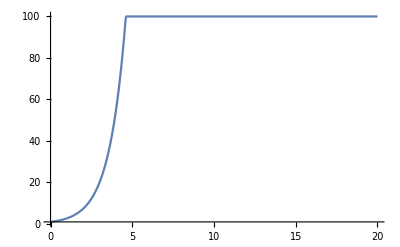

```mathematica
Plot[flogistic[t,1,100,100,1],{t,0,20},PlotRange->Full]
```

```mathematica
D[κ/(1+((κ/y0)^ν - 1) Exp[-α ν t])^(1/ν),α]
```

ⅇ^(-t α ν) t κ (-1+(κ/y0)^ν) (1+ⅇ^(-t α ν) (-1+(κ/y0)^ν))^(-1-1/ν)

```mathematica
falpha[t_,α_,ν_,κ_,y0_]:= ⅇ^(-t α ν) t κ (-1+(κ/y0)^ν) (1+ⅇ^(-t α ν) (-1+(κ/y0)^ν))^(-1-1/ν)
```

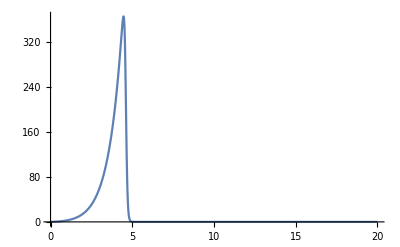

```mathematica
Plot[falpha[t,1,20,100,1],{t,0,20},PlotRange->Full]
```

```mathematica
D[κ/(1+((κ/y0)^ν - 1) Exp[-α ν t])^(1/ν),ν]//FullSimplify
```

1/ν^2 ⅇ^(-t α ν) κ (ⅇ^(-t α ν) (-1+ⅇ^(t α ν)+(κ/y0)^ν))^(-(1+ν)/ν) (t α (-1+(κ/y0)^ν) ν-(κ/y0)^ν ν Log[κ/y0]+(-1+ⅇ^(t α ν)+(κ/y0)^ν) Log[1+ⅇ^(-t α ν) (-1+(κ/y0)^ν)])

```mathematica
fν[t_,α_,ν_,κ_,y0_]:=1/ν^2 ⅇ^(-t α ν) κ (ⅇ^(-t α ν) (-1+ⅇ^(t α ν)+(κ/y0)^ν))^(-(1+ν)/ν) (t α (-1+(κ/y0)^ν) ν-(κ/y0)^ν ν Log[κ/y0]+(-1+ⅇ^(t α ν)+(κ/y0)^ν) Log[1+ⅇ^(-t α ν) (-1+(κ/y0)^ν)])
```

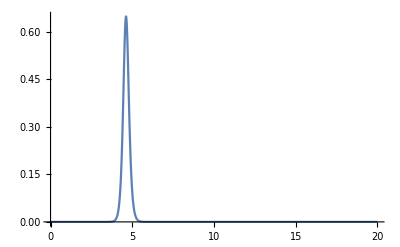

```mathematica
Plot[fν[t,1,10,100,1],{t,0,20},PlotRange->Full]
```

## Elasticities

```mathematica
1/ν^2 ⅇ^(-t α ν) κ (ⅇ^(-t α ν) (-1+ⅇ^(t α ν)+(κ/y0)^ν))^(-(1+ν)/ν) (t α (-1+(κ/y0)^ν) ν-(κ/y0)^ν ν Log[κ/y0]+(-1+ⅇ^(t α ν)+(κ/y0)^ν) Log[1+ⅇ^(-t α ν) (-1+(κ/y0)^ν)])//FullSimplify
```

1/ν^2 ⅇ^(-t α ν) κ (ⅇ^(-t α ν) (-1+ⅇ^(t α ν)+(κ/y0)^ν))^(-(1+ν)/ν) (t α (-1+(κ/y0)^ν) ν-(κ/y0)^ν ν Log[κ/y0]+(-1+ⅇ^(t α ν)+(κ/y0)^ν) Log[1+ⅇ^(-t α ν) (-1+(κ/y0)^ν)])